```mathematica
description="Intermediate calculations";
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Isolated slepton-side diagram

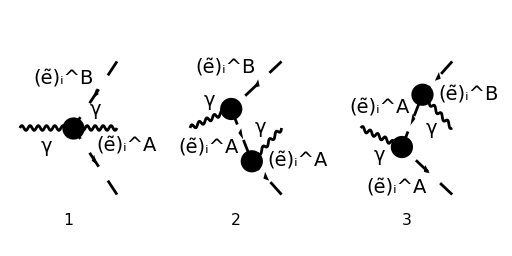

```mathematica
diags=InsertFields[
CreateTopologies[0,1->3],
{V[1]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags,
ColumnsXRows->{3,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)";
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

```mathematica
Mlist=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{q},
OutgoingMomenta->{k1,k,k2},
ChangeDimension->D,
List->True,
DropSumOver->True,
SMP->True
]
```

{2 e^2 g^Lor1Lor2 (ε^*)^Lor2(k) ε^Lor1(q) IndexDelta(A,B),(e^2 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2),(e^2 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(A,2,i))^2)}

```mathematica
M[0]=Total[Mlist]/.{FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1,D],MSf[A,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1,D],MSf[B,2,i]]]} (*FeynCalc chooses to use A-mass in both propagators, so we manually change the one corresponding with radiation from slepton B to a B-mass, although they are equal due to Kronecker delta *)
```

(e^2 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+(e^2 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+2 e^2 g^Lor1Lor2 (ε^*)^Lor2(k) ε^Lor1(q) IndexDelta(A,B)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M[1]=M[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]}
```

(e^2 q^Lor1 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+(e^2 q^Lor1 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+2 e^2 q^Lor1 g^Lor1Lor2 (ε^*)^Lor2(k) IndexDelta(A,B)

```mathematica
M[2]=M[1]//Contract//FeynAmpDenominatorExplicit
```

2 e^2 IndexDelta(A,B) (q·ε^*(k))+(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (k·q+k_1·q-k_2·q))/(2 (k·k_1)+k^2)+(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) (k·q-k_1·q+k_2·q))/(2 (k·k_2)+k^2)

```mathematica
M[3]=M[2]/.{Momentum[q,D]->Momentum[k1+k2+k,D]}
```

(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (k·(k+k_1+k_2)+k_1·(k+k_1+k_2)-k_2·(k+k_1+k_2)))/(2 (k·k_1)+k^2)+(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) (k·(k+k_1+k_2)-k_1·(k+k_1+k_2)+k_2·(k+k_1+k_2)))/(2 (k·k_2)+k^2)+2 e^2 IndexDelta(A,B) ((k+k_1+k_2)·ε^*(k))

```mathematica
M[4]=M[3]//ExpandScalarProduct
```

(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (-(MSf(A,2,i))^2+(MSf(B,2,i))^2+2 (k·k_1)+k^2))/(2 (k·k_1)+k^2)+(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) ((MSf(A,2,i))^2-(MSf(B,2,i))^2+2 (k·k_2)+k^2))/(2 (k·k_2)+k^2)+2 e^2 IndexDelta(A,B) (k·ε^*(k)+k_1·ε^*(k)+k_2·ε^*(k))

```mathematica
M[5]=M[4]//Simplify
```

(2 e^2 IndexDelta(A,B) ((MSf(A,2,i))^2-(MSf(B,2,i))^2) ((k·k_2) (k·ε^*(k)+2 (k_1·ε^*(k)))+k^2 (k_1·ε^*(k)-k_2·ε^*(k))-(k·k_1) (k·ε^*(k)+2 (k_2·ε^*(k)))))/((2 (k·k_1)+k^2) (2 (k·k_2)+k^2))

```mathematica
M[6]=M[5]/.{B->A} (*Can do this for photon case since IndexDelta*)
```

0

### If we exclude 4-point diagram

```mathematica
M23[0]=Total[Mlist[[{2,3}]]]
```

(e^2 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(A,2,i))^2)+(e^2 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
M23[1]=M23[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]};
M23[2]=M23[1]//Contract//FeynAmpDenominatorExplicit;
M23[3]=M23[2]/.{Momentum[q,D]->Momentum[k1+k2+k,D]};
M23[4]=M23[3]//ExpandScalarProduct;
M23[5]=M23[4]//Simplify
```

e^2 IndexDelta(A,B) (-((k·ε^*(k)+2 (k_2·ε^*(k))) ((MSf(A,2,i))^2-(MSf(B,2,i))^2+2 (k·k_2)+k^2))/(2 (k·k_2)+k^2)-(k·ε^*(k))-2 (k_1·ε^*(k)))

```mathematica
M23[6]=M23[5]/.{B->A}
```

e^2 (-2 (k·ε^*(k))-2 (k_1·ε^*(k))-2 (k_2·ε^*(k)))

```mathematica
M1[0]=Mlist[[1]]
```

2 e^2 g^Lor1Lor2 (ε^*)^Lor2(k) ε^Lor1(q) IndexDelta(A,B)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
M1[1]=M1[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]};
M1[2]=M1[1]//Contract//FeynAmpDenominatorExplicit;
M1[3]=M1[2]/.{Momentum[q,D]->Momentum[k1+k2+k,D]};
M1[4]=M1[3]//ExpandScalarProduct;
M1[5]=M1[4]//Simplify
```

2 e^2 IndexDelta(A,B) (k·ε^*(k)+k_1·ε^*(k)+k_2·ε^*(k))

```mathematica
M1[6]=M1[5]/.{B->A}
```

2 e^2 (k·ε^*(k)+k_1·ε^*(k)+k_2·ε^*(k))

Combining them:

```mathematica
Mtot[0]=M1[6]+M23[6]//Simplify
```

0

Thus we see that we must include the 4-point diagram for the Ward identity to hold!

### With Z-boson instead

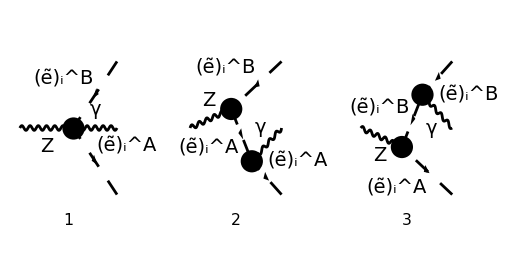

```mathematica
diags=InsertFields[
CreateTopologies[0,1->3],
{V[2]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags,
ColumnsXRows->{3,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{q},
OutgoingMomenta->{k1,k,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
DropSumOver->True,
SMP->True
]//Simplify
```

-1/(2 (cos(θ_W)) (sin(θ_W)))e^2 (ε^*)^Lor2(k) ε^Lor1(q) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2; (*Yes, both are m_A since Kronecker delta*)
SPD[k2]=MSf[A,2,i]^2;
M[1]=M[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]}
```

-1/(2 (cos(θ_W)) (sin(θ_W)))e^2 q^Lor1 (ε^*)^Lor2(k) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2)

```mathematica
M[2]=M[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify
```

-1/(2 (cos(θ_W)) (sin(θ_W)))e^2 q^Lor1 (ε^*)^Lor2(k) (2 (sin(θ_W))^2 A,B-USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2)

```mathematica
M[3]=M[2]/.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}
```

(e^2 ZliAB q^Lor1 (ε^*)^Lor2(k) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2))/((cos(θ_W)) (sin(θ_W)))

```mathematica
M[4]=M[3]//Contract//FeynAmpDenominatorExplicit;
M[5]=M[4]/.{Momentum[q,D]->Momentum[k1+k2+k,D]};
M[6]=M[5]//ExpandScalarProduct;
M[7]=M[6]//Simplify
```

(2 e^2 ZliAB ((MSf(A,2,i))^2-(MSf(B,2,i))^2) ((k·k_2) (k·ε^*(k)+2 (k_1·ε^*(k)))+k^2 (k_1·ε^*(k)-k_2·ε^*(k))-(k·k_1) (k·ε^*(k)+2 (k_2·ε^*(k)))))/((cos(θ_W)) (2 (k·k_1)+k^2) (2 (k·k_2)+k^2) (sin(θ_W)))

Using (4.3) in Tore, and including only the case where A,B not equal since the expression is zero otherwise, we get:

```mathematica
M[8]=M[7]/.{ZliAB->1/2 Cos[θil] Sin[θil]}
```

(e^2 sin(θil) cos(θil) ((MSf(A,2,i))^2-(MSf(B,2,i))^2) ((k·k_2) (k·ε^*(k)+2 (k_1·ε^*(k)))+k^2 (k_1·ε^*(k)-k_2·ε^*(k))-(k·k_1) (k·ε^*(k)+2 (k_2·ε^*(k)))))/((cos(θ_W)) (2 (k·k_1)+k^2) (2 (k·k_2)+k^2) (sin(θ_W)))

## Computing

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
MakeBoxes[m1,TraditionalForm]:="\!\(\*SubscriptBox[\(m\),\(1\)]\)";
MakeBoxes[m2,TraditionalForm]:="\!\(\*SubscriptBox[\(m\),\(2\)]\)";
```

```mathematica
p1l[l_]=Pair[Momentum[p1,D],LorentzIndex[l,D]];
p2l[l_]=Pair[Momentum[p2,D],LorentzIndex[l,D]];
```

```mathematica
k1l[lor_]=Pair[Momentum[k1,D],LorentzIndex[lor,D]];
k2l[lor_]=Pair[Momentum[k2,D],LorentzIndex[lor,D]];
kl[lor_]=Pair[Momentum[k,D],LorentzIndex[lor,D]];
```

```mathematica
K[lor1_,lor2_]=1/(SPD[k2,k])k1l[lor1] k2l[lor2]+1/SPD[k1,k] k1l[lor2] k2l[lor1]+MTD[lor1,lor2];
```

```mathematica
L[l1_,l2_]=K[l1,ρ] K[l2,ρ]//Contract;
L[μ,ν]
```

```mathematica
H[l1_,l2_]=2 p1l[l1] p2l[l2]+2 p2l[l1] p1l[l2] - s MTD[l1,l2];
H[μ,ν]
```

```mathematica
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[p1,p2]=s/2;
```

```mathematica
HL[0]=H[μ,ν]L[μ,ν]//Contract//Simplify
```

### Compare with hand calculation

```mathematica
HLbyHand=SPD[k2]/SPD[k2,k]^2 (4 SPD[p1,k1] SPD[p2,k1]-s SPD[k1])+SPD[k1]/SPD[k1,k]^2 (4 SPD[p1,k2] SPD[p2,k2]-s SPD[k2]) + (2-D) s + (SPD[k1,k2]/(SPD[k1,k] SPD[k2,k])+1/SPD[k1,k]+1/SPD[k2,k]) (4 SPD[p1,k1] SPD[p2,k2] + 4 SPD[p1,k2] SPD[p2,k1] - 2 s SPD[k1,k2])
```

```mathematica
FCCompareResults[HL[0],HLbyHand];
```

### Simplify HL

```mathematica
FCClearScalarProducts[];
HL[1]=HL[0]/.{s->SPD[p1+p2]}//ExpandScalarProduct//Simplify
```

```mathematica
SetMandelstam[x,{p1,p2,-k1,-k2,-k},{0,0,m1,m2,0}];
HL[2]=HL[1]//Simplify
```

```mathematica
MandelstamRules={
x[2,4]->x[3,5]-x[1,2]+m2^2-x[1,4],
x[4,5]->x[1,2]+m1^2+m2^2-x[3,5]-x[3,4],
x[2,3]->2m1^2+m2^2-x[3,5]-x[1,3]-x[3,4]
}
```

```mathematica
HL[3]=HL[2]//.MandelstamRules//Simplify
```

```mathematica
HL[4]=HL[3]/.{
x[1,2]->s,
x[3,4]->Q^2
}//Simplify
```